```mathematica
DSolve[{D[bsq[r],r]==-2*bsq[r]/r*(1 + vroc/(gamma*Delta0/r)),bsq[r0]==bsqr0},bsq[r],r]
```

{{bsq[r]→(bsqr0 ⅇ^(-(2 r vroc)/(Delta0 gamma)+(2 r0 vroc)/(Delta0 gamma)) r0^2)/r^2}}

```mathematica
crap=FullSimplfiy[%]
```

FullSimplfiy[{{bsq[r]→(bsqr0 ⅇ^(-(2 r vroc)/(Delta0 gamma)+(2 r0 vroc)/(Delta0 gamma)) r0^2)/r^2}}]

```mathematica
toplot=crap[[1,1,1,2]]//.{r0->5*10^(13),vroc->0.02,Delta0->10^(10),gamma->700,bsqr0->5.6*10^(10)}
```

(1.4×10^38 ⅇ^(0.285714-5.71429×10^-15 r))/r^2

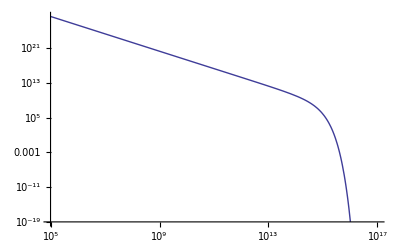

```mathematica
LogLogPlot[toplot,{r,10^5,10^(17)}]
```

```mathematica
DSolve[{D[bsq[r],r]==-2*bsq[r]/r*(1 + vroc/(gamma*Delta0/r)),bsq[r0]==bsqr0},bsq[r],r]
```

{{bsq[r]→(bsqr0 ⅇ^(-(2 r vroc)/(Delta0 gamma)+(2 r0 vroc)/(Delta0 gamma)) r0^2)/r^2}}

```mathematica
rdiss=(Delta0*gamma)/(4*vroc)//.{gamma->700,Delta0->8*10^(10),vroc->0.02}
rdiss=(Delta0*gamma)/(4*vroc)//.{gamma->700,Delta0->8*10^(10),vroc->0.002}
```

7.×10^14

7.×10^15

```mathematica
rdiss=(Delta0*gamma)/(4*vroc)//.{gamma->700,Delta0->3*10^(10),vroc->0.02}
rdiss=(Delta0*gamma)/(4*vroc)//.{gamma->700,Delta0->3*10^(10),vroc->0.002}
```

2.625×10^14

2.625×10^15

```mathematica
lbi0=30.15;
lbi1=29.22;
lb0=lbi0;
bi0=10^lbi0;
bi1=10^lbi1;
biavg=0.5*(bi0+bi1);
b0=bi0;
bavg=(b1+b0)*0.5;
(*vroc=0.297;*)
vroc=0.1;
gammaavg=0.5*(1.157+1.28);
r0=4.43*10^(5);
r1=9.186*10^(5)
ravg=0.5*( r0+r1);
lpavg=0.5*(1.377*10^6+2.57*10^6);
lr0=Log[10,r0]
lr1=Log[10,r1]
A=4*vroc*ravg/(gammaavg*lpavg)
mylb1a=lb0+10^(0.5*(lbi1+lbi0))/(10^(0.5*(lb1+lb0)))*(lbi1-lbi0)-A*(lr1-lr0);
solsa=Solve[lb1==mylb1a,lb1]
mylb1b=lb0+biavg/(0.5*(b0+10^lb1))*(lbi1-lbi0)-A*(lr1-lr0);
solsb=FindRoot[mylb1b==lb1,{lb1,lbi1}]
```

918600.

5.6464

5.96313

0.113244

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{lb1→29.2681+0.241768 ⅈ}}

{lb1→29.1743}

```mathematica
mylb1a//.solsa[[1]]
mylb1a//.solsa[[2]]
```

29.2681+0.241768 ⅈ

Part::partw: Part 2 of {{lb1 → 29.268092340968654`  + 0.24176785436593468` ⅈ}} does not exist.

ReplaceRepeated::reps: {{{lb1 → 29.268092340968654`  + 0.24176785436593468` ⅈ}} ⟦ 2 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

30.1141-4.5028×10^29 10^(-0.5 (30.15+lb1))//.{{lb1→29.2681+0.241768 ⅈ}}⟦2⟧

```mathematica
mylb1b//.solsb[[1]]
```

29.1743

```mathematica
Anorm=4*vroc*bavg/(gammaavg*lpavg)
myb1=b0+(bi1-bi0)-Anorm*(r1-r0)
solsnorm=Solve[b1==myb1,b1]
Log[10,solsnorm[[1,1,2]]]
```

8.31701×10^-8 (1.41254×10^30+b1)

1.65959×10^29-0.0395557 (1.41254×10^30+b1)

{{b1→1.05896×10^29}}

29.0249

```mathematica
Clear[A,lr0,lbsq0,r0]
```

```mathematica
bsqideal[lr_]:=Exp[lbsq0]*(Exp[lr]/Exp[lr0])^(-n)
dlbsqidealdlogr[lr_]:=Module[{foo,foo2,rx},
foo=D[bsqideal[rx],rx]/bsqideal[rx];
foo2=foo//.{rx->r};
foo2
];
sols=DSolve[{D[lfun[lr],lr]==dlbsqidealdlogr[lr]*bsqideal[lr]/Exp[lfun[lr]]-Ait,lfun[lr0]==lbsq0},lfun[lr],lr]
sols=FullSimplify[sols]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{lfun[lr]→-Ait lr+Log[(ⅇ^(lr-lr0))^-n (ⅇ^(lbsq0+Ait lr)-(Ait ⅇ^(lbsq0+Ait lr))/(Ait-n)+(Ait ⅇ^(lbsq0+Ait lr0+lr n-lr0 n))/(Ait-n))]}}

{{lfun[lr]→-Ait lr+Log[((ⅇ^(lr-lr0))^-n (-Ait ⅇ^(lbsq0+Ait lr0+lr n-lr0 n)+ⅇ^(lbsq0+Ait lr) n))/(-Ait+n)]}}

```mathematica
mylfun=-Ait lr+Log[((ⅇ^(lr-lr0))^-n (-Ait ⅇ^(lbsq0+Ait lr0+lr n-lr0 n)+ⅇ^(lbsq0+Ait lr) n))/(-Ait+n)]
myfun=FullSimplify[FullSimplify[Exp[mylfun],{lr>0,Ait>0,n>0,lbsq0>0,lr0>0}]//.{lr0->Log[r0],lbsq0->Log[bsq0],lr->Log[r]},{r>0,Ait>0,n>0,bsq0>0,r0>0}]
```

-Ait lr+Log[((ⅇ^(lr-lr0))^-n (-Ait ⅇ^(lbsq0+Ait lr0+lr n-lr0 n)+ⅇ^(lbsq0+Ait lr) n))/(-Ait+n)]

(bsq0 (Ait (r0/r)^Ait-n (r0/r)^n))/(Ait-n)

```mathematica
consts={vrocnew->10^(-4),Ait->4*vrocnew/(700*Pi/2*0.02),r0->10^6,lr0->Log[r0],lbsq0->Log[bsq0],bsq0->10^30.15} 
(*consts={A->0,lr0->Log[10^6],lbsq0->Log[10^30.15]};*)
```

{vrocnew→1/10000,Ait→0.181891 vrocnew,r0→1000000,lr0→Log[r0],lbsq0→Log[bsq0],bsq0→1.41254×10^30}

```mathematica
toplot=lfun[lr]//.sols[[1]]//.consts
```

-2.00002 lr+Log[-0.500005 (-2.82508×10^42 ⅇ^(0.0000181891 lr)+2.56928×10^25 ⅇ^(0.000251292+2 lr))]

```mathematica
toplot2=Log[bsqideal[lr]]//.consts
```

Log[1.41254×10^42 ⅇ^(-2 lr)]

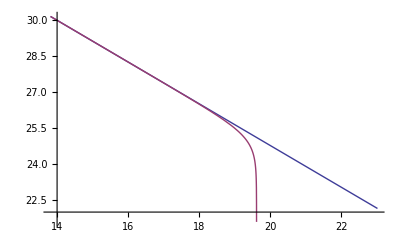

```mathematica
Plot[{Log[10,Exp[toplot2]],Log[10,Exp[toplot]]},{lr,Log[10^6],Log[10^(10)]}]
```

```mathematica
otherconsts={n->2}
consts=Join[consts,otherconsts]
```

{n→2}

{vrocnew→1/10000,Ait→0.181891 vrocnew,r0→1000000,lr0→Log[r0],lbsq0→Log[bsq0],bsq0→1.41254×10^30,n→2}

```mathematica
bsqidealr[r_]:=bsq0*(r/r0)^(-n)
dbsqidealdr[r_]:=Module[{foo,foo2,rx},
foo=D[bsqidealr[rx],rx];
foo2=foo//.{rx->r};
foo2
];
Afunc[r_]:=2*Ait/(1+r/(r-r0));
solsr1=DSolve[{D[bsq[r],r]==D[bsqidealr[r],r]-Afunc[r]/r*bsq[r],bsq[r0]==bsq0},bsq[r],r]
solsr2=DSolve[{D[bsq[r],r]==D[bsqidealr[r],r]-Ait/r*bsq[r],bsq[r0]==bsq0},bsq[r],r]
solsr3=DSolve[{D[bsq[r],r]==-2*bsqidealr[r]/r-Ait/r*bsq[r],bsq[r0]==bsq0},bsq[r],r]
solsr4=DSolve[{D[bsq[r],r]==-2*bsq[r]/r-Ait/r*bsq[r],bsq[r0]==bsq0},bsq[r],r]
solsr5=DSolve[{D[bsq[r],r]==-4*vroco*bsq[r]/(gamma*r*deltaor),bsq[r0]==bsq0},bsq[r],r]

solsB1=DSolve[{D[bsq[r],r]==D[bsqidealr[r],r]-Ait*bsq[r],bsq[r0]==bsq0},bsq[r],r]
```

{{bsq[r]→1/(2 Ait-n)bsq0 ⅇ^(2 Ait (-Log[2 r]+1/2 Log[2 r-r0])-2 Ait (Log[r0]/2-Log[2 r0])) (2 r-r0)^-Ait (r/r0)^-n (2 Ait (2 r-r0)^Ait (r/r0)^n-n (2 r-r0)^Ait (r/r0)^n+(-4)^Ait ⅇ^(2 Ait (Log[r0]/2-Log[2 r0])) n (2 r-r0)^Ait (r/r0)^n r0^Ait Hypergeometric2F1[Ait,2 Ait-n,1+2 Ait-n,2]-4^Ait ⅇ^(2 Ait (Log[r0]/2-Log[2 r0])) n r^(2 Ait) (1-(2 r)/r0)^Ait Hypergeometric2F1[Ait,2 Ait-n,1+2 Ait-n,(2 r)/r0])}}

{{bsq[r]→(bsq0 r^-Ait (r/r0)^-n (-n r^Ait+Ait (r/r0)^n r0^Ait))/(Ait-n)}}

{{bsq[r]→(bsq0 r^-Ait (r/r0)^-n (-2 r^Ait+2 (r/r0)^n r0^Ait+Ait (r/r0)^n r0^Ait-n (r/r0)^n r0^Ait))/(Ait-n)}}

{{bsq[r]→bsq0 r^(-2-Ait) r0^(2+Ait)}}

{{bsq[r]→bsq0 r^(-(4 vroco)/(deltaor gamma)) r0^((4 vroco)/(deltaor gamma))}}

{{bsq[r]→bsq0 ⅇ^(-Ait r) (r/r0)^-n (ⅇ^(Ait r0) (r/r0)^n+n (-Ait r)^n Gamma[-n,-Ait r]-n (r/r0)^n (-Ait r0)^n Gamma[-n,-Ait r0])}}

```mathematica
mysolsB1=FullSimplify[bsq[r]//.solsB1[[1]],{Ait>0,r>r0,r0>0,n>0}]
```

bsq0 ⅇ^(-Ait r) (ⅇ^(Ait r0)+n (r0/r)^n ExpIntegralE[1+n,-Ait r]-n ExpIntegralE[1+n,-Ait r0])

1.41254×10^30 ⅇ^(-0.0000181891 r) ((8.99466×10^7+1039.38 ⅈ)+(2000000000000 ExpIntegralE[3,-0.0000181891 r])/r^2)

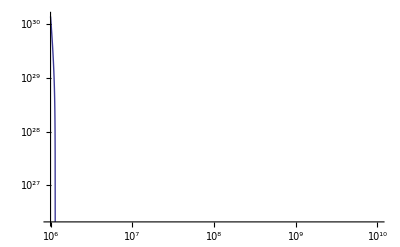

```mathematica
toplot=mysolsB1//.consts
LogLogPlot[toplot,{r,10^6,10^(10)}]
```

```mathematica
mybsq=bsq[r]//.solsr4[[1]]
```

bsq0 r^(-2-Ait) r0^(2+Ait)

```mathematica
FullSimplify[-D[mybsq,r]+-2*bsqidealr[r]/r-Ait/r*mybsq]
```

bsq0 (-(2 (r/r0)^-n)/r+2 r^(-3-Ait) r0^(2+Ait))

```mathematica
mybsqofr=bsq[r]//.solsr1[[1]]//.{r0->Exp[lr0],bsq0->Exp[lbsq0]}//.consts
```

-1/(r^2 (-1000000+2 r)^0.0000181891)7.06282×10^41 ⅇ^(0.000276508+0.0000363783 (-Log[2 r]+1/2 Log[-1000000+2 r])) ((-3.99996×10^-12+2.2857×10^-16 ⅈ) r^2 (-1000000+2 r)^0.0000181891-1.9995 (1-r/500000)^0.0000181891 r^0.0000363783 Hypergeometric2F1[-1.99996,0.0000181891,-0.999964,r/500000])

```mathematica
toplot1=Log[10,bsqidealr[Exp[lr]]]//.{r0->Exp[lr0],bsq0->Exp[lbsq0]}//.consts
toplot2=Log[10,mybsqofr]//.{r->Exp[lr],r0->Exp[lr0],bsq0->Exp[lbsq0]}//.consts
```

Log[1.41254×10^42 ⅇ^(-2 lr)]/Log[10]

1/Log[10]Log[-1/((-1000000+2 ⅇ^lr)^0.0000181891)7.06282×10^41 ⅇ^(0.000276508-2 lr+0.0000363783 (-Log[2 ⅇ^lr]+1/2 Log[-1000000+2 ⅇ^lr])) ((-3.99996×10^-12+2.2857×10^-16 ⅈ) ⅇ^(2 lr) (-1000000+2 ⅇ^lr)^0.0000181891-1.9995 (ⅇ^lr)^0.0000363783 (1-ⅇ^lr/500000)^0.0000181891 Hypergeometric2F1[-1.99996,0.0000181891,-0.999964,ⅇ^lr/500000])]

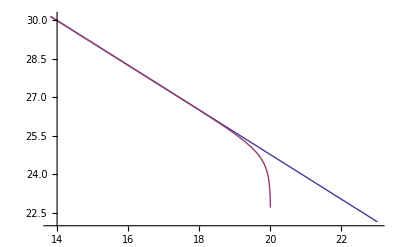

```mathematica
Plot[{toplot1,toplot2},{lr,Log[10^6],Log[10^(10)]}]
```